# Fourier Elephant

## Draw

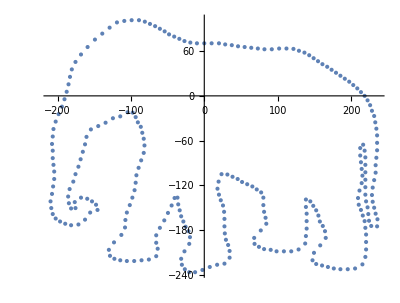

```mathematica
img=Import["https://i.stack.imgur.com/wtJoA.png"];
img=Binarize[img~ColorConvert~"Grayscale"~ImageResize~500~Blur~3];
pts=DeleteDuplicates@Cases[Normal@ListContourPlot[Reverse@ImageData[img],Contours->{0.5}],_Line,-1][[1,1]];
center=Mean@MinMax[pts]&/@Transpose@pts;
pts=#-center&/@pts[[;;;;20]];
elephantPlot=ListPlot[pts,AspectRatio->Automatic]
```

## Complex Stuff

```mathematica
(*get Fourier coefficients*)
z = pts[[All,1]] + I*pts[[All,2]]; (*array of complex numbers in time domain*)
```

```mathematica
L = Length[z];
```

```mathematica
m=15;
```

```mathematica
(*cnf0 = 1 /L*Table[Sum[z[[k]]*Exp[-I*2Pi*i*k/L],{k,1,L}],{i,-m,m}];
{f[t_], g[t_]}=ReIm[Sum[cnf0[[j]]*Exp[I*2Pi*t*(j-m-1)],{j,1,2m+1}]];
Manipulate[ParametricPlot[{f[t], g[t]}, {t,0,s}, PlotRange->250], {s,0.001,1}]
Clear[m,f,g]
steplot[ m_]:=Module[{cnfo,f,g, steplot},
						cnfo= 1 /L*Table[Sum[z[[k]]*Exp[-I*2Pi*i*k/L],{k,1,L}],{i,-m,m}];
						{f[t_],g[t_]}= ReIm[Sum[cnfo[[j]]*Exp[I*2Pi*t*(j-m-1)],{j,1,2m+1}]];
						ParametricPlot[{f[t], g[t]}, {t,0,1}, AspectRatio->Automatic]]
Manipulate[steplot[m],{m,1,30,1}]*)
```

```mathematica
epycicles[s_]:=Module[{cnfo, centers, indexes, orders, truecenters, raggi},
						cnfo= 1 /L*Table[Sum[z[[k]]*Exp[-I*2Pi*i*k/L],{k,1,L}],{i,-m,m}];
						centers[t_]= Table[cnfo[[j]]*Exp[I*2Pi*t*(j-m-1)],{j,1,2m+1}];
						indexes= Flatten@Table[{m+i,i},{i,1,m}];
						AppendTo[indexes, 2m+1];
						orders[t_]=centers[t][[indexes]];
						raggi = Table[Abs@cnfo[[indexes]][[j]],{j,1,2m+1}];
						truecenters[t_]= Accumulate@orders[t];
						{truecenters[t], raggi} ]
```

```mathematica
centri[t_]=Table[ReIm[epycicles[t][[1]][[j]]],{j,1,2m+1}];
```

```mathematica
raggi=epycicles[t][[2]];
```

```mathematica
pallini=Table[{Green, PointSize[0.02], Point[centri[t][[i]]]},{i,1,2m+1}];
```

```mathematica
cerchi = Table[ {Blue,Thickness[0.005],  Circle[centri[t][[i]],raggi[[i]]]},{i,1,2m}];
```

```mathematica
linee = Table[{Cyan, Line[{centri[t][[j]], centri[t][[j+1]]}]}, {j, 1, 2m}];
```

```mathematica
background = {White, Thickness[0.003], Rectangle[{-400,-400},{400,200}]};
```

```mathematica
total[t_] = Graphics[Join[ background, pallini,cerchi ,linee]];
```

```mathematica
film = Table[Show[total[s], ParametricPlot[centri[t][[2m+1]], {t,0,s} ]], {s, 0.001,1, 0.01}];
```

```mathematica
Export["elephant.gif", film , "ControlAppearance"->None, "AnimationRepetitions"->∞]
```

elephant.gif

## Movie

```mathematica
ListAnimate[film]
```